注意：
	物理量的计算请带单位（用 Quantity 或 Ctrl = 组合键实现）。
	代入计算数据请尽可能用 Around[x,δ] 的形式呈现，有助于不确定度分析。
	计算单个输入用 Shift+ Enter组合键 ；或者用 Evaluation→Evaluate Notebook 重新计算整个文件。

```mathematica
dsPre=Quantity[{0.601,0.599,0.609,0.610,0.605,0.611},"Millimeters"];(*为dsPre定义一组测量值,Quantity可以为其赋单位*)
ds=dsPre-Quantity[-0.029, "Millimeters"];(*修正零点误差*)
DataAnalyze[ds,Quantity[0.004, "Millimeters"]](*一键实现数据分析，第二参数为B类不确定度*)
```

平均值 | 0.634833 mm
标准差 | 0.00499667 mm
样本标准偏差 | 0.00547357 mm
合成不确定度 | 0.00677938 mm
结果表达 | (0.6350.007) mm
相对合成不确定度 | 1.068%数据特征

```mathematica
d=Quantity[(0.6350.007), "Millimeters"];(*尽量用复制粘贴的方式将结果数据赋值给d。*)
lens=Quantity[{{15.0,16.5,18.1,19.7,21.1,22.8},{24.1,25.9,27.2,29.0,30.2,31.9}},"Millimeters"];(*定义二维数组（含两个子数组），用于逐差法*)
DataAnalyzeInDifferences[lens](*专用于逐差法的数据分析。第二参数不填则意味着不考虑B类不确定度*)
```

平均值 | 1.53056 mm
标准差 | 0.132916 mm
样本标准偏差 | 0.145602 mm
合成不确定度 | 0.145602 mm
结果表达 | (1.530.15) mm
相对合成不确定度 | 9.513%数据特征

```mathematica
nN=Quantity[(1.530.15), "Millimeters"];(*同样需要复制粘贴；因为N在Mathematica中已有定义，故用nN代之*)
g=Quantity[9.8015, ("Meters")/("Seconds")^2];(*网络查询知当地重力加速度*)
m=Quantity[0.5, "Kilograms"];(*重量分度*)
L=Around[Quantity[722, "Millimeters"],Quantity[3, "Millimeters"]];(*Around函数可以为某个值赋不确定度*)
nD=Around[Quantity[683, "Millimeters"],Quantity[3, "Millimeters"]];(*D在Mathematica中已有定义，故用nD代之*)
b=Around[Quantity[49.8, "Millimeters"],Quantity[0.5, "Millimeters"]];(*以上数据同样用Ctrl =组合键输入*)
(8m g L nD)/(π d^2 b nN)//UnitConvert(*直接求出最终结果，自带不确定度。UnitConver将其转化为SI单位制*)
```

2.000.2010^11 kg/(m s^2)

```mathematica
%//UnitSimplify(*将上一个运算结果进行单位简化，不保证SI*)
```

2.000.2010^11 Pa

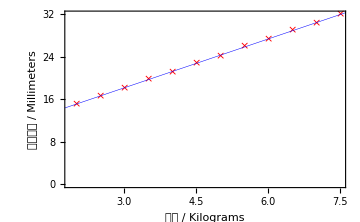
-Graphics-   自变量均值x̄ | 4.75 kg
因变量均值ȳ | 23.4583 mm
纵截距â | 8.88613 mm
斜率b̂ | 3.06783 mm/kg
线性回归估计公式 |  ŷ=8.88613+3.06783 x
相关系数r | 0.999815
y标准偏差s(y) | 0.111657 mm
b标准偏差s(b) | 0.0646904 mm/kg
a标准偏差s(a) | 0.326937 mm线性回归分析

```mathematica
datas=QuantityArray[{{2.00,15.0},{2.50,16.5},{3.00,18.1},{3.50,19.7},{4.00,21.1},{4.50,22.8},{5.00,24.1},{5.50,25.9},{6.0,27.2},{6.50,29.0},{7.00,30.2},{7.50,31.9}},{"Kilograms","Millimeters"}];(*用QuantityArray定义一组带单位的点*)
LinearAnalyze[datas,"重量","标尺长度"](*一键实现线性回归分析*)
```

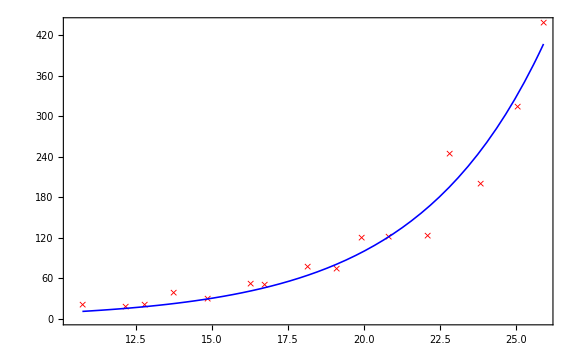
指数型 曲线拟合方程：
ŷ=0.867641 ⅇ^(0.237386 x)
-Graphics-曲线拟合分析

```mathematica
dataexp=QuantityArray[{{10.75,19.89},{12.16,16.42},{12.77,19.91},{13.75,38.45},{14.85,28.86},{16.26,51.81},{16.73,49.64},{18.15,76.62},{19.08,73.64},{19.93,119.2},{20.81,121.4},{22.07,122.9},{22.80,243.7},{23.84,199.3},{25.05,313.2},{25.91,437.0}},{"Seconds","Meters"}];(*定义一组数据，它们可能满足指数关系*)
CurveAnalyze[dataexp,"exp"](*用指数函数尝试拟合，注意"exp"字段*)
```

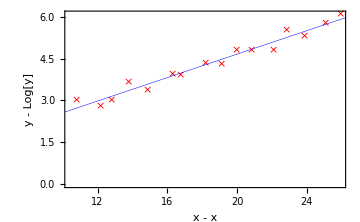
-Graphics-   自变量均值x̄ | 18.4319
因变量均值OverBar[Log[y]] | 4.33069
纵截距â | Log[0.456638]
斜率b̂ | 0.210182
线性回归估计公式 | Log[y]=Log[0.456638]+0.210182 x
相关系数r | 0.9824线性化回归分析

```mathematica
CurveLinearizeAnalyze[dataexp,"exp"](*将数据化为线性后再分析，注意"exp"字段*)
```

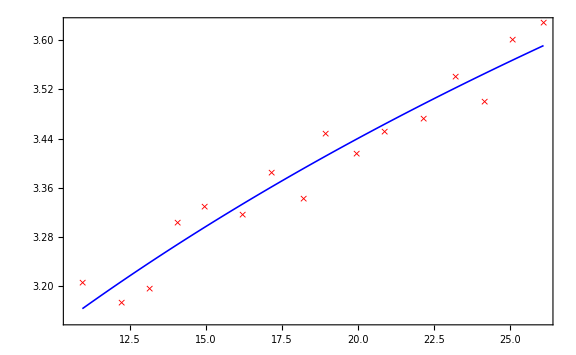
对数型 曲线拟合方程：
ŷ=Log[14.5491+0.832663 x]
-Graphics-曲线拟合分析

```mathematica
datalog=QuantityArray[{{10.93,3.204},{12.20,3.172},{13.14,3.195},{14.06,3.302},{14.92,3.328},{16.18,3.316},{17.14,3.383},{18.18,3.341},{18.91,3.447},{19.92,3.415},{20.85,3.450},{22.14,3.472},{23.19,3.540},{24.16,3.499},{25.06,3.600},{26.10,3.627}},{"Seconds","Meters"}];(*定义一组数据，它们可能满足对数关系*)
CurveAnalyze[datalog,"log"](*用对数函数尝试拟合，注意"log"字段*)
```

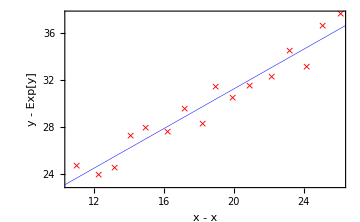
-Graphics-   自变量均值x̄ | 18.5675
因变量均值OverBar[ⅇ^y] | 30.0296
纵截距â | 14.3305
斜率b̂ | 0.845514
线性回归估计公式 | ⅇ^y=14.3305+0.845514 x
相关系数r | 0.969301线性化回归分析

```mathematica
CurveLinearizeAnalyze[datalog,"log"](*同上*)
```

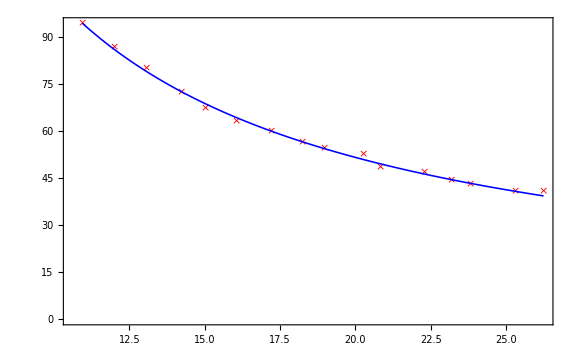
幂函数型 曲线拟合方程：
ŷ=1038.23/x^1.00214
-Graphics-曲线拟合分析

```mathematica
datapow=QuantityArray[{{10.94,94.30},{12.01,86.67},{13.07,80.19},{14.22,72.35},{15.02,67.16},{16.05,63.15},{17.19,60.06},{18.22,56.40},{18.95,54.61},{20.27,52.49},{20.81,48.36},{22.27,46.72},{23.19,44.22},{23.82,42.95},{25.29,40.64},{26.24,40.61}},{"Seconds","Meters"}];(*定义一组数据，它们可能满足反比例（幂函数）关系*)
CurveAnalyze[datapow,"pow"](*注意"pow"字段*)
```

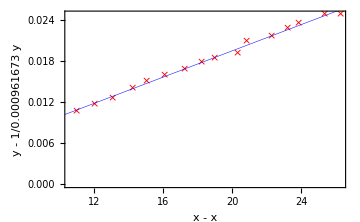
-Graphics-   自变量均值x̄ | 18.5975
因变量均值OverBar[y^(1/0.000961673)] | 0.0181608
纵截距â | 0
斜率b̂ | 0.99215
线性回归估计公式 | y=1038.23/x^1.00214
相关系数r | 0.997565线性化回归分析

```mathematica
CurveLinearizeAnalyze[datapow,"pow"](*同上*)
```

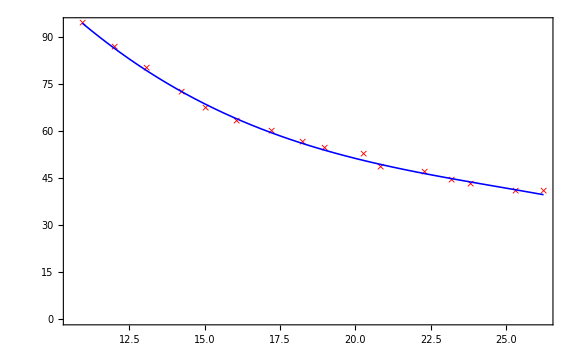
3次多项式 曲线拟合方程：
ŷ=252.195-22.1373 x+0.82732 x^2-0.0111407 x^3
-Graphics-曲线拟合分析

```mathematica
CurveAnalyze[datapow,"poly3"](*尝试用3次多项式拟合。除此之外还可使用"poly5","poly12","poly30"字段*)
```